## Text Analysis

```mathematica
text="I am feeling peaceful. Watched the sun rise and heard the birds chirp a beautiful good morning song. I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing. Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring. Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.";
```

```mathematica
sentences = TextCases[text,"Sentence"]
```

{I am feeling peaceful.,Watched the sun rise and heard the birds chirp a beautiful good morning song.,I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing.,Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring.,Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.}

```mathematica
ClearAll[i]
```

```mathematica
(* take in paragraph, output how many sentences are respectively Positive, Negative, Neutral *)
countSentiments[ text_String ] := Module[{sentences , classifyResults, countPos,countNeg,countNeut, countsAssociation},

sentences = TextCases[text, "Sentence"];

classifyResults = Classify["Sentiment", sentences];

countsAssociation = Counts [classifyResults];

countPos = countsAssociation["Positive"];
countNeg = countsAssociation["Negative"];
countNeut = countsAssociation["Neutral"];
{countPos, countNeg, countNeut} /. _Missing -> 0

];
```

```mathematica
(* take in paragraph, output how many sentences are respectively Positive, Negative, Neutral with associations *)
countSentimentsAssociation[ text_String ] := Module[{sentences , classifyResults, countPos,countNeg,countNeut, countsAssociation},

sentences = TextCases[text, "Sentence"];

classifyResults = Classify["Sentiment", sentences];

countsAssociation = Counts [classifyResults]


];

(* create pie chart of sentiments *)
createPieChart [ text_String ] := PieChart[ countSentimentsAssociation[text],  ChartLabels -> Automatic];

(* create bar chart of sentiments *)
createBarChart [ text_String ] := BarChart[ countSentimentsAssociation[text],  ChartLabels -> Automatic];
```

```mathematica
countSentiments["I am happy. I am sad. I am cold."]
```

{2,1,0}

```mathematica
countSentimentsAssociation["I am happy. I am sad. I am cold."]
```

<|Positive→2,Negative→1|>

```mathematica
PieChart[countSentimentsAssociation["I am happy. I am sad. I am cold."],  ChartLabels -> Automatic]
```

-Graphics-

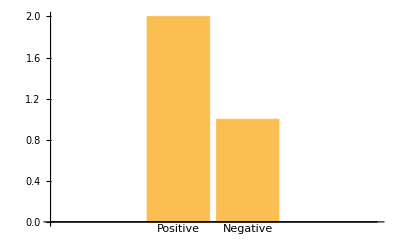

```mathematica
createBarChart [ "I am happy. I am sad. I am cold." ]
```

```mathematica
(* Make a list of only the Positive sentences in a paragraph. *)
posSentences[ text_String ] := Module[{sentences, posList, classifyResults},

sentences = TextCases[text, "Sentence"];
posList = {};

classifyResults = Classify["Sentiment", sentences];
For[i=1,i≤ Length[sentences],i++, If[Classify["Sentiment",sentences[[i]]]=="Positive",
																					AppendTo [posList,sentences[[i]]] , Nothing]];
posList
];

(* Make a list of only the Negative sentences in a paragraph. *)
negSentences[ text_String ] := Module[{sentences, negList, classifyResults},

sentences = TextCases[text, "Sentence"];
negList = {};

classifyResults = Classify["Sentiment", sentences];
For[i=1,i≤ Length[sentences],i++, If[Classify["Sentiment",sentences[[i]]]=="Negative",
																					AppendTo [negList,sentences[[i]]] , Nothing]];
negList
];
		
(* Make a list of only the Neutral sentences in a paragraph. *)
neutSentences[ text_String ] := Module[{sentences, neutList, classifyResults},

sentences = TextCases[text, "Sentence"];
neutList = {};

classifyResults = Classify["Sentiment", sentences];
For[i=1,i≤ Length[sentences],i++, If[Classify["Sentiment",sentences[[i]]]=="Neutral",
																					AppendTo [neutList,sentences[[i]]] , Nothing]];
neutList
];
```

```mathematica
posSentences["I love puppies. I can fly. I am crying."]
```

{I love puppies.}

```mathematica
negSentences["I love puppies. I can fly. I am crying."]
```

{I am crying.}

```mathematica
neutSentences["I love puppies. I can fly. I am crying."]
```

{I can fly.}

```mathematica
(* Extract the nouns from only Positive sentences in a paragraph. *)
posNouns[ text_String] := Module[{sentences, words, posNouns},

sentences = posSentences[text];
posNouns = Flatten[TextCases[#, "Noun"] & /@ sentences];																																	
						
DeleteStopwords[posNouns]
]

(* Extract the verbs from only Positive sentences in a paragraph. *)
posVerbs[ text_String] := Module[{sentences, words, posVerbs},
sentences = posSentences[text];
posVerbs = Flatten[TextCases[#, "Verb"] & /@ sentences];																																		
						
DeleteStopwords[posVerbs]
]

(* Extract the nouns from only Negative sentences in a paragraph. *)
negNouns[ text_String] := Module[{sentences, words, negNouns},

sentences = negSentences[text];
negNouns = Flatten[TextCases[#, "Noun"] & /@ sentences];																																	
						
DeleteStopwords[negNouns]
]

(* Extract the verbs from only Negative sentences in a paragraph. *)
negVerbs[ text_String] := Module[{sentences, words, negVerbs},
sentences = negSentences[text];
negVerbs = Flatten[TextCases[#, "Verb"] & /@ sentences];																																		
						
DeleteStopwords[negVerbs]
]

(* Extract the nouns from only Neutral sentences in a paragraph. *)
neutNouns[ text_String] := Module[{sentences, words, neutNouns},

sentences = negSentences[text];
neutNouns = Flatten[TextCases[#, "Noun"] & /@ sentences];																																	
						
DeleteStopwords[neutNouns]
]

(* Extract the verbs from only Neutral sentences in a paragraph. *)
neutVerbs[ text_String] := Module[{sentences, words, neutVerbs},
sentences = neutSentences[text];
neutVerbs = Flatten[TextCases[#, "Verb"] & /@ sentences];																																		
						
DeleteStopwords[neutVerbs]
]
```

```mathematica
testText = "I like puppies. I like cats. I am eating. I am sleepy. I hate frogs. I hate spiders. I don't like driving. I am sad.";
```

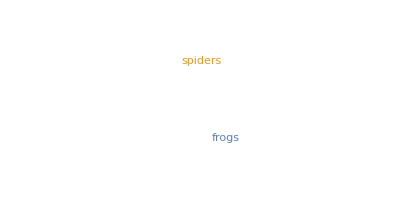

```mathematica
WordCloud[neutNouns[testText]]
```

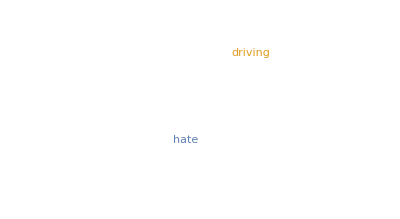

```mathematica
WordCloud[negVerbs[testText]]
```

```mathematica
(* Make graph of probabilities *)
graphPosSentimentProb [text_String]:= Module[{sentences},

sentences = posSentences[text];

Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]]
]
```

```mathematica
graphPosSentimentProb[testText]
```

{0.446588,0.440576,0.598538,0.566871}

```mathematica
ListLinePlot
```

```mathematica
(* Make word clouds that show negative nouns and verbs, pos, neutral also *)
```

```mathematica
(* Make a time series of the number of positive and negative words per day. *)
```

```mathematica
(* Make a pie chart with 3 colors displaying negative, positive, and neutral sentiment sentences, then label *)
```

```mathematica
(* make bar chart of activities that made you happy today *)
(* make scatterplot of probabilities of postive sentencces *)
(* export data inputted into report *)
```

```mathematica
(* Make graph of categories of words like in the text analyis lecture *)
```

```mathematica
(* From text analysis lecture code: Get a GloVe (Global Vectors) word embedding model and run it: *)
```

```mathematica
glove = NetModel[
"GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

```mathematica
glove[text]
```

{{-0.046539,0.61966,0.56647,-0.46584,-1.189,0.44599,0.066035,86,0.28374,-0.70931,0.15003,-0.2154,-0.37616,-0.032502,0.8062},92,{1}}
 |  |  |  |

```mathematica
Dimensions[text]
```

{}

```mathematica
displayWordClouds [text_]:= Grid[{{Labeled[WordCloud[negVerbs[text]],Style["Negative Verbs",18,Bold],Top],WordCloud[negVerbs[testText]]},
{WordCloud[negVerbs[testText]],WordCloud[negVerbs[testText]]}}]
```

```mathematica
{,],,},{,,,},{,, ,
```

```mathematica
Grid[{{"Positive actions: ",WordCloud[posVerbs[#text]],"Positive influences: ",WordCloud[posNouns[#text]]},{"Negative actions: ",WordCloud[negVerbs[#text]],"Negative influences: ",WordCloud[negNouns[#text]]},{"Neutral actions: ",WordCloud[neutVerbs[#text]],"Neutral influences: ",WordCloud[neutNouns[#text]]},{"Pie","PieChart","Selfie: ","Picture"}}]
```

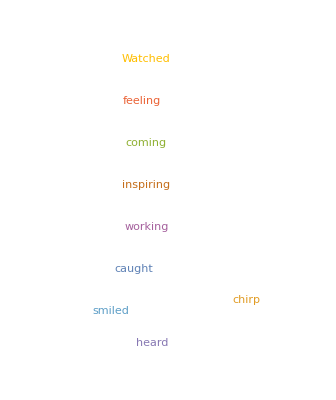
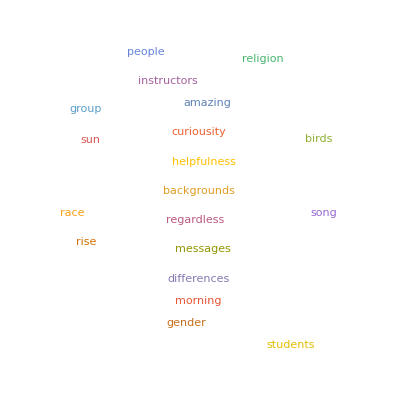
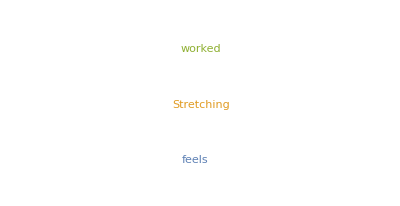
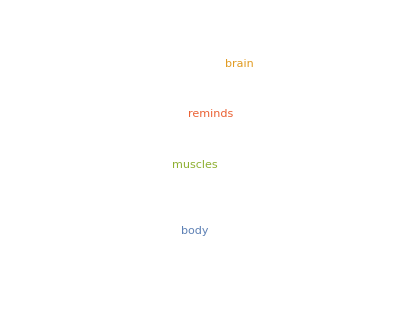
Positive actions:  | -Graphics- | Positive influences:  | -Graphics-
Negative actions:  | -Graphics- | Negative influences:  | -Graphics-
Neutral actions:  | -Graphics- | Neutral influences:  | -Graphics-
Pie | PieChart | Selfie:  | Picture

```mathematica
Grid[{{"Positive actions: ",WordCloud[posVerbs[text]],"Positive influences: ",WordCloud[posNouns[text]]},{"Negative actions: ",WordCloud[negVerbs[text]],"Negative influences: ",WordCloud[negNouns[text]]},{"Neutral actions: ",WordCloud[neutVerbs[text]],"Neutral influences: ",WordCloud[neutNouns[text]]},{"Pie","PieChart","Selfie: ","Picture"}}]
```

### Microsite

```mathematica
grid [text_,image_]:=Grid[{{Labeled[WordCloud[negVerbs[text]],Style["Negative Verbs",18,Bold],Top],WordCloud[negVerbs[testText]]},
{WordCloud[negVerbs[testText]],WordCloud[negVerbs[testText]]}}]
```

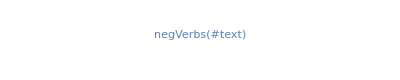
-Graphics-Negative Verbs | -Graphics-
-Graphics- | -Graphics-

```mathematica
grid [#text,#image]
```

```mathematica
Grid[{{Grid[{{1,2},{3,4},{5,6},{7,8}}],Column[{1,2,3}]}},Spacings-> 2]
```

1 | 2
3 | 4
5 | 6
7 | 8 | 1
2
3

```mathematica
Head[-Graphics-]
```

```mathematica
None ==None
```

True

```mathematica
If[ Head[-Graphics-] === None, "No Selfie",
Column@{Classify["FacialExpression", -Graphics-],-Graphics-}]
```

sadness
-Graphics-

```mathematica
ImageResize[-Graphics-,100]
```

-Graphics-

```mathematica
Labeled[Style["Hearty",FontFamily->"Arial Rounded MT Bold",Bold,FontColor->Pink,60],-Graphics-,Left]
```

Hearty-Graphics-

```mathematica
Rasterize[Labeled[Style["Hearty",FontFamily->"Arial Rounded MT Bold",Bold,FontColor->Pink,60],-Graphics-,Left],RasterSize->Large]
```

```mathematica
ImageResize[-Graphics-,300]
```

-Graphics-

```mathematica
Row[{-Graphics-,Style["  Hearty",FontFamily->"Arial Rounded MT Bold",Bold,FontColor->Pink,40]}]
```

-Graphics-  Hearty

```mathematica
CloudDeploy[

FormPage[{{"text","Daily log:"} ->"String" ,
{"image","Selfie of the day:"} -><|"Interpreter"->"Image","Required"-> False, "Default"->None|>},

Grid[{{"Positive actions: ",WordCloud[posVerbs[#text]],"Positive influences: ",WordCloud[posNouns[#text]]},{"Negative actions: ",WordCloud[negVerbs[#text]],"Negative influences: ",WordCloud[negNouns[#text]]},{"Neutral actions: ",WordCloud[neutVerbs[#text]],"Neutral influences: ",WordCloud[neutNouns[#text]]},{"Pie chart: ",createPieChart[#text],"Selfie: ",If[ #image === None, "No Selfie",
Column@{Classify["FacialExpression", #image],#image}]}}]&,
AppearanceRules-> <|"Title"->-Graphics-,"Description"->"Welcome to Hearty! This is a fun website meant to help you reflect on your day based on a daily log describing how you are feeling and a picture of yourself.  "|>]

,"Hearty"
, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/clloo/Hearty]

```mathematica
(* microsite v2 *)
```

```mathematica
CloudDeploy[

FormPage[{{"text","Please input a daily log describing how you are feeling and what you have been up to:"} ->"String" ,
{"image","Please copy and paste your selfie of the day here:"} -><|"Interpreter"->"Image","Required"-> False, "Default":>None|>},

Grid[{{"Positive actions: ",WordCloud[posVerbs[#text]],"Positive influences: ",WordCloud[posNouns[#text]]},{"Negative actions: ",WordCloud[negVerbs[#text]],"Negative influences: ",WordCloud[negNouns[#text]]},{"Neutral actions: ",WordCloud[neutVerbs[#text]],"Neutral influences: ",WordCloud[neutNouns[#text]]},{"Pie chart: ",createPieChart[#text],"Selfie: ",If[ #image == None, "No Selfie",
Column[{Classify["FacialExpression", #image],#image}]]
}}]&,
AppearanceRules-> <|"Title"->-Graphics-,"Description"->"Hearty"|>]

,"Hearty"
, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/clloo/Hearty]

```mathematica
(* Working microsite code: *)
```

```mathematica
CloudDeploy[

FormPage[{{"text","Please input a daily log describing how you are feeling and what you have been up to:"} ->"String" ,
{"image","Please copy and paste your selfie of the day here:"} -><|"Interpreter"->"Image","Required"-> False, "Default":>None|>},

Column[{ createPieChart[#text],
If[ #image == None, "No Selfie",
Column[{Classify["FacialExpression", #image],#image}]]
}]&,

AppearanceRules-> <|"Title"->-Graphics-,"Description"->"Hearty"|>]

,"Hearty"
, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/clloo/Hearty]

```mathematica
Classify["FacialExpression", #image]
```

```mathematica
Face
```

```mathematica
url dispatcher
```

### Other Stuff

```mathematica
testSentences = TextCases["I am happy. I am sad. I am cold.","Sentence"]
```

{I am happy.,I am sad.,I am cold.}

```mathematica
Classify["Sentiment", testSentences, "Probabilities"][[All,"Positive"]]
```

{0.915166,0.241839,0.496866}

```mathematica
CountSentiments["I am happy. I am sad. I am cold."]
```

{2,1,0}

```mathematica
PieChart[%]
```

-Graphics-

Last modified on: Tuesday, July 10, 2018 at 11:44

## Scratch Work

```mathematica
Counts[Classify["Sentiment",sentences]]
```

<|Positive→4,Negative→1|>

```mathematica
Mean@Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]]
```

0.7445

```mathematica
Classify["Sentiment", sentences, "Probabilities"][[All,"Neutral"]]
```

{0.113184,0.0337055,0.0497827,0.233479,0.138568}

```mathematica
Map[PartOfSpeech,{"dog","eat"}][[1]][[1]]
```

noun